## Ricci flat field equations

```mathematica
eq1=r*a[r]*b[r]*a''[r]-r*a[r]*a'[r]*b'[r]+2*a[r]*b[r]*a'[r];
eq2=r*b[r]*a''[r]-b'[r]*(r(a'[r]+2*a[r]));
eq3=a[r]*(b[r])^3-r*(b[r]*a'[r]-a[r]*b'[r]);
FullSimplify[eq1==0]
FullSimplify[eq2==0]
FullSimplify[eq3==0]
```

a[r] (a'[r] (2 b[r]-r b'[r])+r b[r] a''[r])==0

r (2 a[r]+a'[r]) b'[r]==r b[r] a''[r]

r b[r] a'[r]==a[r] (b[r]^3+r b'[r])

```mathematica
FullSimplify[DSolve[{eq1==0,eq2==0},{a[r],b[r]},{r}]]
```

{{a[r]→ⅇ^((2 ArcTan[(-1+2 r C[1])/(√(-1-2 C[1]))])/(√(-1-2 C[1]))) C[2],b[r]→(ⅇ^((2 ArcTan[(-1+2 r C[1])/(√(-1-2 C[1]))])/(√(-1-2 C[1]))) r^2 C[3])/(1+2 r-2 r^2 C[1])}}

# Harmonic Curvature

```mathematica
eq1=(r)^2*a[r]*(b[r])^2*a'''[r]+3*(r)^2*a[r]*a'[r]*(b'[r])^2-(r)^2*a[r]*b[r]*a'[r]*b''[r]-2*a[r]*(b[r])^2*a'[r]-a''[r]*((r)^2*(b[r])^2*a'[r]-2*r*a[r]*(b[r])^2)+b'[r]*((r)^2*b[r]*(a'[r])^2-3*(r)^2*a[r]*b[r]*a''[r]-2*r*a[r]*b[r]*a'[r]);
eq2=(a[r])^2*(b[r])^4-r^2*(b[r])^2*(a'[r])^2-r^2*a[r]*b[r]*a'[r]*b'[r]+3*r^2*(a[r])^2*(b'[r])^2-r^2*(a[r])^2*b[r]*b''[r]-(a[r])^2*(b[r])^2;
FullSimplify[eq1==0]
FullSimplify[eq2==0]
```

r^2 b[r] a'[r] (-a'[r] b'[r]+b[r] a''[r])+a[r] (-3 r^2 a'[r] b'[r]^2+r b[r] (b'[r] (2 a'[r]+3 r a''[r])+r a'[r] b''[r])+b[r]^2 (2 a'[r]-r (2 a''[r]+r a^(3)[r])))==0

a[r]^2 (-b[r]^2+b[r]^4+3 r^2 b'[r]^2-r^2 b[r] b''[r])==r^2 b[r] a'[r] (b[r] a'[r]+a[r] b'[r])

## Numerical solution?

NDSolve::ndsz: At r == 2.7241×10^-15, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At r == 1.47725, step size is effectively zero; singularity or stiff system suspected.

{{a[r]→InterpolatingFunction[…][r],b[r]→InterpolatingFunction[…][r]}}

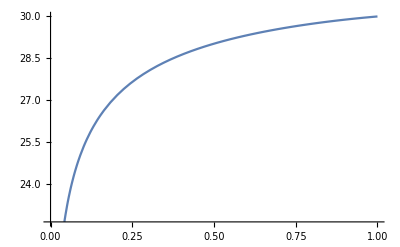

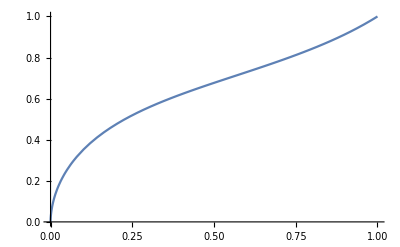

```mathematica
s=NDSolve[{eq1==0,eq2==0,a[1]==30,a'[1]==1,a'''[1]==1,b[1]==1,b'[1]==1},{a[r],b[r]},{r,0,10}]
Plot[Evaluate[{a[r],a'[r]}/. s],{r,0,1}]
Plot[Evaluate[{b[r],b'[r]}/. s],{r,0,1}]
```

## As a dynamical system?

```mathematica
ds1=eq1/.{b[r]->b,b'[r]->β,b''[r]->β',a[r]->a,a'[r]->α,a''[r]->α',a'''[r]->α''}
ds2=eq2/.{b[r]->b,b'[r]->β,b''[r]->β',a[r]->a,a'[r]->α,a''[r]->α',a'''[r]->α''}
```

-2 a b^2 α+3 a r^2 α β^2-(-2 a b^2 r+b^2 r^2 α) α'+β (-2 a b r α+b r^2 α^2-3 a b r^2 α')-a b r^2 α β'+a b^2 r^2 α''

-a^2 b^2+a^2 b^4-b^2 r^2 α^2-a b r^2 α β+3 a^2 r^2 β^2-a^2 b r^2 β'

```mathematica
ds1f=ds1/.{α->α,α'->A,α''->A'}
ds2f=ds2/.{α->α,α'->A,α''->A'}
```

-2 a b^2 α-A (-2 a b^2 r+b^2 r^2 α)+(-3 a A b r^2-2 a b r α+b r^2 α^2) β+3 a r^2 α β^2+a b^2 r^2 A'-a b r^2 α β'

-a^2 b^2+a^2 b^4-b^2 r^2 α^2-a b r^2 α β+3 a^2 r^2 β^2-a^2 b r^2 β'

```mathematica
FullSimplify[Solve[ds1f==0,A']]
FullSimplify[Solve[ds2f==0,β']]
```

{{A'→((2 b^2 (-A r+α))/r^2+b (3 A+(2 α)/r) β-3 α β^2+(b α (A b-α β))/a+b α β')/b^2}}

{{β'→-b/r^2+b^3/r^2-(b α^2)/a^2-(α β)/a+(3 β^2)/b}}

```mathematica
FullSimplify[Solve[ds1f==0,A']]
FullSimplify[%/.{β'->-b/r^2+b^3/r^2-(b α^2)/a^2-(α β)/a+(3 β^2)/b}]
```

{{A'→((2 b^2 (-A r+α))/r^2+b (3 A+(2 α)/r) β-3 α β^2+(b α (A b-α β))/a+b α β')/b^2}}

{{A'→-α^3/a^2+(α (A b-2 α β))/(a b)+(α (b+b^3+2 r β)+A r (-2 b+3 r β))/(b r^2)}}

## Power-law solutions?

```mathematica
a[r_]=Sum[Subscript[a, j]*r^j,{j,0,5}];
b[r_]=Sum[Subscript[b, j]*r^j,{j,0,5}];
Series[FullSimplify[eq1],{r,0,5}]
```

-2 (a_0 a_1 b_0^2)-2 (a_1^2 b_0^2+3 a_0 a_1 b_0 b_1) r+(-4 a_1 a_2 b_0^2+12 a_0 a_3 b_0^2-5 a_1^2 b_0 b_1-10 a_0 a_2 b_0 b_1-a_0 a_1 b_1^2-10 a_0 a_1 b_0 b_2) r^2-4 (a_2^2 b_0^2-a_1 a_3 b_0^2-10 a_0 a_4 b_0^2+4 a_1 a_2 b_0 b_1+a_0 a_2 b_1^2+2 a_1^2 b_0 b_2+6 a_0 a_2 b_0 b_2+4 a_0 a_1 b_0 b_3) r^3+(-6 a_2 a_3 b_0^2+26 a_1 a_4 b_0^2+90 a_0 a_5 b_0^2-14 a_2^2 b_0 b_1-12 a_1 a_3 b_0 b_1+36 a_0 a_4 b_0 b_1-3 a_1 a_2 b_1^2-3 a_0 a_3 b_1^2-30 a_1 a_2 b_0 b_2-30 a_0 a_3 b_0 b_2+3 a_1^2 b_1 b_2-10 a_0 a_2 b_1 b_2+4 a_0 a_1 b_2^2-13 a_1^2 b_0 b_3-42 a_0 a_2 b_0 b_3-24 a_0 a_1 b_0 b_4) r^4-2 (3 a_3^2 b_0^2-4 a_2 a_4 b_0^2-34 a_1 a_5 b_0^2+17 a_2 a_3 b_0 b_1-7 a_1 a_4 b_0 b_1-55 a_0 a_5 b_0 b_1+2 a_2^2 b_1^2+2 a_1 a_3 b_1^2-4 a_0 a_4 b_1^2+12 a_2^2 b_0 b_2+20 a_1 a_3 b_0 b_2+8 a_0 a_4 b_0 b_2+a_1 a_2 b_1 b_2+9 a_0 a_3 b_1 b_2-3 a_1^2 b_2^2+25 a_1 a_2 b_0 b_3+33 a_0 a_3 b_0 b_3-2 a_1^2 b_1 b_3+8 a_0 a_2 b_1 b_3-7 a_0 a_1 b_2 b_3+10 a_1^2 b_0 b_4+32 a_0 a_2 b_0 b_4+a_0 a_1 b_1 b_4+17 a_0 a_1 b_0 b_5) r^5+O[r]^6

## first branch

```mathematica
Subscript[a, 0]=0;
Series[FullSimplify[eq1],{r,0,6}]
```

-2 (a_1^2 b_0^2) r+(-4 a_1 a_2 b_0^2-5 a_1^2 b_0 b_1) r^2-4 (a_2^2 b_0^2-a_1 a_3 b_0^2+4 a_1 a_2 b_0 b_1+2 a_1^2 b_0 b_2) r^3+(-6 a_2 a_3 b_0^2+26 a_1 a_4 b_0^2-14 a_2^2 b_0 b_1-12 a_1 a_3 b_0 b_1-3 a_1 a_2 b_1^2-30 a_1 a_2 b_0 b_2+3 a_1^2 b_1 b_2-13 a_1^2 b_0 b_3) r^4-2 (3 a_3^2 b_0^2-4 a_2 a_4 b_0^2-34 a_1 a_5 b_0^2+17 a_2 a_3 b_0 b_1-7 a_1 a_4 b_0 b_1+2 a_2^2 b_1^2+2 a_1 a_3 b_1^2+12 a_2^2 b_0 b_2+20 a_1 a_3 b_0 b_2+a_1 a_2 b_1 b_2-3 a_1^2 b_2^2+25 a_1 a_2 b_0 b_3-2 a_1^2 b_1 b_3+10 a_1^2 b_0 b_4) r^5+(-8 a_3 a_4 b_0^2+40 a_2 a_5 b_0^2-27 a_3^2 b_0 b_1-22 a_2 a_4 b_0 b_1+74 a_1 a_5 b_0 b_1-13 a_2 a_3 b_1^2+3 a_1 a_4 b_1^2-66 a_2 a_3 b_0 b_2-34 a_1 a_4 b_0 b_2-6 a_2^2 b_1 b_2-12 a_1 a_3 b_1 b_2+10 a_1 a_2 b_2^2-38 a_2^2 b_0 b_3-76 a_1 a_3 b_0 b_3-4 a_1 a_2 b_1 b_3+19 a_1^2 b_2 b_3-76 a_1 a_2 b_0 b_4+3 a_1^2 b_1 b_4-29 a_1^2 b_0 b_5) r^6+O[r]^7

```mathematica
Subscript[b, 0]=0;
Series[FullSimplify[eq1],{r,0,6}]
```

3 (-a_1 a_2 b_1^2+a_1^2 b_1 b_2) r^4-2 (2 a_2^2 b_1^2+2 a_1 a_3 b_1^2+a_1 a_2 b_1 b_2-3 a_1^2 b_2^2-2 a_1^2 b_1 b_3) r^5+(-13 a_2 a_3 b_1^2+3 a_1 a_4 b_1^2-6 a_2^2 b_1 b_2-12 a_1 a_3 b_1 b_2+10 a_1 a_2 b_2^2-4 a_1 a_2 b_1 b_3+19 a_1^2 b_2 b_3+3 a_1^2 b_1 b_4) r^6+O[r]^7

```mathematica
Solve[-Subscript[a, 1] Subscript[a, 2] Subscript[b, 1]^2+Subscript[a, 1]^2 Subscript[b, 1] Subscript[b, 2]==0,Subscript[a, 2]]
```

{{a_2→(a_1 b_2)/b_1}}

```mathematica
Subscript[a, 2]=(Subscript[a, 1] Subscript[b, 2])/Subscript[b, 1];
Series[FullSimplify[eq1],{r,0,6}]
```

-4 (a_1 a_3 b_1^2-a_1^2 b_1 b_3) r^5+((3 a_1 a_4 b_1^3-25 a_1 a_3 b_1^2 b_2+4 a_1^2 b_2^3+15 a_1^2 b_1 b_2 b_3+3 a_1^2 b_1^2 b_4) r^6)/b_1+O[r]^7

```mathematica
Solve[Subscript[a, 1] Subscript[a, 3] Subscript[b, 1]^2-Subscript[a, 1]^2 Subscript[b, 1] Subscript[b, 3]==0,Subscript[a, 1] ]
```

{{a_1→0},{a_1→(a_3 b_1)/b_3}}

```mathematica
Subscript[a, 1]=(Subscript[a, 3] Subscript[b, 1])/Subscript[b, 3];
Series[FullSimplify[eq1],{r,0,6}]
```

((4 a_3^2 b_1 b_2^3+3 a_3 a_4 b_1^3 b_3-10 a_3^2 b_1^2 b_2 b_3+3 a_3^2 b_1^3 b_4) r^6)/b_3^2+O[r]^7

```mathematica
Solve[((4 Subscript[a, 3]^2 Subscript[b, 1] Subscript[b, 2]^3+3 Subscript[a, 3] Subscript[a, 4] Subscript[b, 1]^3 Subscript[b, 3]-10 Subscript[a, 3]^2 Subscript[b, 1]^2 Subscript[b, 2] Subscript[b, 3]+3 Subscript[a, 3]^2 Subscript[b, 1]^3 Subscript[b, 4]) r^6)/Subscript[b, 3]^2==0,Subscript[a, 4]]
```

{{a_4→-(a_3 (4 b_2^3-10 b_1 b_2 b_3+3 b_1^2 b_4))/(3 b_1^2 b_3)}}

```mathematica
Subscript[a, 4]=-(Subscript[a, 3] (4 Subscript[b, 2]^3-10 Subscript[b, 1] Subscript[b, 2] Subscript[b, 3]+3 Subscript[b, 1]^2 Subscript[b, 4]))/(3 Subscript[b, 1]^2 Subscript[b, 3]);
Series[FullSimplify[eq1],{r,0,6}]
```

O[r]^7

```mathematica
Series[FullSimplify[eq2],{r,0,6}]
```

((a_3^2 b_1^6+a_3^2 b_1^2 b_2^2-2 a_3^2 b_1^3 b_3) r^6)/b_3^2+O[r]^7

```mathematica
Solve[((Subscript[a, 3]^2 Subscript[b, 1]^6+Subscript[a, 3]^2 Subscript[b, 1]^2 Subscript[b, 2]^2-2 Subscript[a, 3]^2 Subscript[b, 1]^3 Subscript[b, 3]) r^6)/Subscript[b, 3]^2==0,Subscript[b, 3]]
```

{{b_3→(b_1^4+b_2^2)/(2 b_1)}}

```mathematica
Subscript[b, 3]=(Subscript[b, 1]^4+Subscript[b, 2]^2)/(2 Subscript[b, 1]);
Series[FullSimplify[eq2],{r,0,6}]
```

O[r]^7

```mathematica
a[r]
b[r]
```

r^3 a_3+r^5 a_5+(2 r a_3 b_1^2)/(b_1^4+b_2^2)+(2 r^2 a_3 b_1 b_2)/(b_1^4+b_2^2)-(2 r^4 a_3 (4 b_2^3-5 b_2 (b_1^4+b_2^2)+3 b_1^2 b_4))/(3 b_1 (b_1^4+b_2^2))

r b_1+r^2 b_2+(r^3 (b_1^4+b_2^2))/(2 b_1)+r^4 b_4+r^5 b_5

```mathematica
FullSimplify[r*a[r]*b[r]*a''[r]-r*a[r]*a'[r]*b'[r]+2*a[r]*b[r]*a'[r]]
FullSimplify[r*b[r]*a''[r]-b'[r]*(r(a'[r]+2*a[r]))]
FullSimplify[a[r]*(b[r])^3-r*(b[r]*a'[r]-a[r]*b'[r])]
```

1/(18 b_1^3 (b_1^4+b_2^2)^2)r^2 (3 r^4 a_5 b_1 (b_1^4+b_2^2)+a_3 (6 b_1^3+3 r^2 b_1^5+10 r^3 b_1^4 b_2+3 r^2 b_1 b_2^2+2 r^3 b_2^3+6 r b_1^2 (b_2-r^2 b_4))) (15 r^4 a_5 b_1 (b_1^4+b_2^2) (10 b_1^2+3 r^2 b_1^4+3 r^2 b_2^2+2 b_1 (4 r b_2+2 r^3 b_4+r^4 b_5))+a_3 (48 r^2 b_1^7+9 r^4 b_1^9+80 r^5 b_1^8 b_2+16 r^5 b_2^5+r^4 b_1 b_2^3 (57 b_2+16 r^2 b_4)+2 b_1^5 (6+129 r^4 b_2^2+40 r^6 b_2 b_4)+12 b_1^4 (4 r b_2+8 r^5 b_2^3-3 r^3 (6 b_4+r b_5))-24 b_1^3 (-3 r^2 b_2^2+2 r^6 b_4^2+r^4 b_2 (7 b_4+2 r b_5))-2 r^3 b_1^2 b_2^2 (-50 b_2+3 r^2 (8 b_4+3 r b_5))-2 b_1^6 (-178 r^3 b_2+3 r^5 (8 b_4+3 r b_5))))

-1/(6 b_1^2 (b_1^4+b_2^2))r (-6 r (10 r^3 a_5 b_1 (b_1^4+b_2^2)+a_3 (3 r b_1^5+20 r^2 b_1^4 b_2+3 r b_1 b_2^2+4 r^2 b_2^3+2 b_1^2 (b_2-6 r^2 b_4))) (2 b_1^2+r^2 b_1^4+r^2 b_2^2+2 r b_1 (b_2+r^2 (b_4+r b_5)))+(3 r^4 (5+2 r) a_5 b_1 (b_1^4+b_2^2)+a_3 (6 (1+2 r) b_1^3+3 r^2 (3+2 r) b_1^5+20 r^3 (2+r) b_1^4 b_2+3 r^2 (3+2 r) b_1 b_2^2+4 r^3 (2+r) b_2^3+12 r b_1^2 ((1+r) b_2-r^2 (2+r) b_4))) (2 b_1^2+3 r^2 b_1^4+3 r^2 b_2^2+2 b_1 (2 r b_2+r^3 (4 b_4+5 r b_5))))

1/(24 b_1^4 (b_1^4+b_2^2))(8 r^5 b_1^2 (-3 r a_5 b_1 (b_1^4+b_2^2) (4 b_1^2+r^2 b_1^4+r^2 b_2^2+b_1 (3 r b_2+r^3 b_4))+a_3 (-((6 b_1^2+r^2 b_1^4+4 r b_1 b_2+r^2 b_2^2) (5 b_1^4 b_2+b_2^3-6 b_1^2 b_4))+2 r b_1 (12 b_1^3+3 r^2 b_1^5+5 r^3 b_1^4 b_2+3 r^2 b_1 b_2^2+r^3 b_2^3+b_1^2 (9 r b_2-3 r^3 b_4)) b_5))+r^3 (3 r^5 a_5 b_1 (b_1^4+b_2^2)+r a_3 (6 b_1^3+3 r^2 b_1^5+10 r^3 b_1^4 b_2+3 r^2 b_1 b_2^2+2 r^3 b_2^3+6 r b_1^2 (b_2-r^2 b_4))) (2 b_1^2+r^2 b_1^4+r^2 b_2^2+2 r b_1 (b_2+r^2 (b_4+r b_5)))^3)

## second branch

```mathematica
Subscript[a, 1]=0;
Series[FullSimplify[eq1],{r,0,5}]
```

2 (6 a_0 a_3 b_0^2-5 a_0 a_2 b_0 b_1) r^2-4 (a_2^2 b_0^2-10 a_0 a_4 b_0^2+a_0 a_2 b_1^2+6 a_0 a_2 b_0 b_2) r^3+(-6 a_2 a_3 b_0^2+90 a_0 a_5 b_0^2-14 a_2^2 b_0 b_1+36 a_0 a_4 b_0 b_1-3 a_0 a_3 b_1^2-30 a_0 a_3 b_0 b_2-10 a_0 a_2 b_1 b_2-42 a_0 a_2 b_0 b_3) r^4-2 (3 a_3^2 b_0^2-4 a_2 a_4 b_0^2+17 a_2 a_3 b_0 b_1-55 a_0 a_5 b_0 b_1+2 a_2^2 b_1^2-4 a_0 a_4 b_1^2+12 a_2^2 b_0 b_2+8 a_0 a_4 b_0 b_2+9 a_0 a_3 b_1 b_2+33 a_0 a_3 b_0 b_3+8 a_0 a_2 b_1 b_3+32 a_0 a_2 b_0 b_4) r^5+O[r]^6

```mathematica
Solve[6 Subscript[a, 0] Subscript[a, 3] Subscript[b, 0]^2-5 Subscript[a, 0] Subscript[a, 2] Subscript[b, 0] Subscript[b, 1]==0,Subscript[b, 1]]
```

{{b_1→(6 a_3 b_0)/(5 a_2)}}

```mathematica
Subscript[b, 1]=(6 Subscript[a, 3] Subscript[b, 0])/(5 Subscript[a, 2]);
Series[FullSimplify[eq1],{r,0,5}]
```

-(4 (25 a_2^3 b_0^2+36 a_0 a_3^2 b_0^2-250 a_0 a_2 a_4 b_0^2+150 a_0 a_2^2 b_0 b_2) r^3)/(25 a_2)-(6 (95 a_2^3 a_3 b_0^2+18 a_0 a_3^3 b_0^2-180 a_0 a_2 a_3 a_4 b_0^2-375 a_0 a_2^2 a_5 b_0^2+175 a_0 a_2^2 a_3 b_0 b_2+175 a_0 a_2^3 b_0 b_3) r^4)/(25 a_2^2)-(2 (657 a_2^2 a_3^2 b_0^2-100 a_2^3 a_4 b_0^2-144 a_0 a_3^2 a_4 b_0^2-1650 a_0 a_2 a_3 a_5 b_0^2+300 a_2^4 b_0 b_2+270 a_0 a_2 a_3^2 b_0 b_2+200 a_0 a_2^2 a_4 b_0 b_2+1065 a_0 a_2^2 a_3 b_0 b_3+800 a_0 a_2^3 b_0 b_4) r^5)/(25 a_2^2)+O[r]^6

```mathematica
Solve[(4 (25 Subscript[a, 2]^3 Subscript[b, 0]^2+36 Subscript[a, 0] Subscript[a, 3]^2 Subscript[b, 0]^2-250 Subscript[a, 0] Subscript[a, 2] Subscript[a, 4] Subscript[b, 0]^2+150 Subscript[a, 0] Subscript[a, 2]^2 Subscript[b, 0] Subscript[b, 2]) r^3)/(25 Subscript[a, 2])==0,Subscript[b, 2] ]
```

{{b_2→-((25 a_2^3+36 a_0 a_3^2-250 a_0 a_2 a_4) b_0)/(150 a_0 a_2^2)}}

```mathematica
Subscript[b, 2]=-((25 Subscript[a, 2]^3+36 Subscript[a, 0] Subscript[a, 3]^2-250 Subscript[a, 0] Subscript[a, 2] Subscript[a, 4]) Subscript[b, 0])/(150 Subscript[a, 0] Subscript[a, 2]^2);
Series[FullSimplify[eq1],{r,0,5}]
```

((-395 a_2^3 a_3 b_0^2+144 a_0 a_3^3 b_0^2-670 a_0 a_2 a_3 a_4 b_0^2+2250 a_0 a_2^2 a_5 b_0^2-1050 a_0 a_2^3 b_0 b_3) r^4)/(25 a_2^2)-(2 (-750 a_2^6 b_0^2+8100 a_0 a_2^3 a_3^2 b_0^2-972 a_0^2 a_3^4 b_0^2+5500 a_0 a_2^4 a_4 b_0^2+3870 a_0^2 a_2 a_3^2 a_4 b_0^2+5000 a_0^2 a_2^2 a_4^2 b_0^2-24750 a_0^2 a_2^2 a_3 a_5 b_0^2+15975 a_0^2 a_2^3 a_3 b_0 b_3+12000 a_0^2 a_2^4 b_0 b_4) r^5)/(375 (a_0 a_2^3))+O[r]^6

```mathematica
Solve[((-395 Subscript[a, 2]^3 Subscript[a, 3] Subscript[b, 0]^2+144 Subscript[a, 0] Subscript[a, 3]^3 Subscript[b, 0]^2-670 Subscript[a, 0] Subscript[a, 2] Subscript[a, 3] Subscript[a, 4] Subscript[b, 0]^2+2250 Subscript[a, 0] Subscript[a, 2]^2 Subscript[a, 5] Subscript[b, 0]^2-1050 Subscript[a, 0] Subscript[a, 2]^3 Subscript[b, 0] Subscript[b, 3]) r^4)/(25 Subscript[a, 2]^2)==0,Subscript[b, 3]]
```

{{b_3→-((395 a_2^3 a_3-144 a_0 a_3^3+670 a_0 a_2 a_3 a_4-2250 a_0 a_2^2 a_5) b_0)/(1050 a_0 a_2^3)}}

```mathematica
Subscript[b, 3]=-((395 Subscript[a, 2]^3 Subscript[a, 3]-144 Subscript[a, 0] Subscript[a, 3]^3+670 Subscript[a, 0] Subscript[a, 2] Subscript[a, 3] Subscript[a, 4]-2250 Subscript[a, 0] Subscript[a, 2]^2 Subscript[a, 5]) Subscript[b, 0])/(1050 Subscript[a, 0] Subscript[a, 2]^3);
Series[FullSimplify[eq1],{r,0,5}]
```

((10500 a_2^6 b_0^2-29265 a_0 a_2^3 a_3^2 b_0^2-17064 a_0^2 a_3^4 b_0^2-77000 a_0 a_2^4 a_4 b_0^2+88530 a_0^2 a_2 a_3^2 a_4 b_0^2-70000 a_0^2 a_2^2 a_4^2 b_0^2-132750 a_0^2 a_2^2 a_3 a_5 b_0^2-168000 a_0^2 a_2^4 b_0 b_4) r^5)/(2625 a_0 a_2^3)+O[r]^6

```mathematica
Solve[((10500 Subscript[a, 2]^6 Subscript[b, 0]^2-29265 Subscript[a, 0] Subscript[a, 2]^3 Subscript[a, 3]^2 Subscript[b, 0]^2-17064 Subscript[a, 0]^2 Subscript[a, 3]^4 Subscript[b, 0]^2-77000 Subscript[a, 0] Subscript[a, 2]^4 Subscript[a, 4] Subscript[b, 0]^2+88530 Subscript[a, 0]^2 Subscript[a, 2] Subscript[a, 3]^2 Subscript[a, 4] Subscript[b, 0]^2-70000 Subscript[a, 0]^2 Subscript[a, 2]^2 Subscript[a, 4]^2 Subscript[b, 0]^2-132750 Subscript[a, 0]^2 Subscript[a, 2]^2 Subscript[a, 3] Subscript[a, 5] Subscript[b, 0]^2-168000 Subscript[a, 0]^2 Subscript[a, 2]^4 Subscript[b, 0] Subscript[b, 4]) r^5)/(2625 Subscript[a, 0] Subscript[a, 2]^3)==0,Subscript[b, 4]]
```

{{b_4→((10500 a_2^6-29265 a_0 a_2^3 a_3^2-17064 a_0^2 a_3^4-77000 a_0 a_2^4 a_4+88530 a_0^2 a_2 a_3^2 a_4-70000 a_0^2 a_2^2 a_4^2-132750 a_0^2 a_2^2 a_3 a_5) b_0)/(168000 a_0^2 a_2^4)}}

```mathematica
Subscript[b, 4]=((10500 Subscript[a, 2]^6-29265 Subscript[a, 0] Subscript[a, 2]^3 Subscript[a, 3]^2-17064 Subscript[a, 0]^2 Subscript[a, 3]^4-77000 Subscript[a, 0] Subscript[a, 2]^4 Subscript[a, 4]+88530 Subscript[a, 0]^2 Subscript[a, 2] Subscript[a, 3]^2 Subscript[a, 4]-70000 Subscript[a, 0]^2 Subscript[a, 2]^2 Subscript[a, 4]^2-132750 Subscript[a, 0]^2 Subscript[a, 2]^2 Subscript[a, 3] Subscript[a, 5]) Subscript[b, 0])/(168000 Subscript[a, 0]^2 Subscript[a, 2]^4);
Series[FullSimplify[eq1],{r,0,5}]
```

O[r]^6

```mathematica
Series[FullSimplify[eq2],{r,0,5}]
```

$Aborted

```mathematica
b[r]
```

b_0+(6 r a_3 b_0)/(5 a_2)-(r^2 (25 a_2^3+36 a_0 a_3^2-250 a_0 a_2 a_4) b_0)/(150 a_0 a_2^2)-(r^3 (395 a_2^3 a_3-144 a_0 a_3^3+670 a_0 a_2 a_3 a_4-2250 a_0 a_2^2 a_5) b_0)/(1050 a_0 a_2^3)+(r^4 (10500 a_2^6-29265 a_0 a_2^3 a_3^2-17064 a_0^2 a_3^4-77000 a_0 a_2^4 a_4+88530 a_0^2 a_2 a_3^2 a_4-70000 a_0^2 a_2^2 a_4^2-132750 a_0^2 a_2^2 a_3 a_5) b_0)/(168000 a_0^2 a_2^4)+r^5 b_5

## third branch

```mathematica
Subscript[b, 0]=0;
Series[FullSimplify[eq1],{r,0,5}]
```

-a_0 a_1 b_1^2 r^2-4 (a_0 a_2 b_1^2) r^3+(-3 a_1 a_2 b_1^2-3 a_0 a_3 b_1^2+3 a_1^2 b_1 b_2-10 a_0 a_2 b_1 b_2+4 a_0 a_1 b_2^2) r^4-2 (2 a_2^2 b_1^2+2 a_1 a_3 b_1^2-4 a_0 a_4 b_1^2+a_1 a_2 b_1 b_2+9 a_0 a_3 b_1 b_2-3 a_1^2 b_2^2-2 a_1^2 b_1 b_3+8 a_0 a_2 b_1 b_3-7 a_0 a_1 b_2 b_3+a_0 a_1 b_1 b_4) r^5+O[r]^6

```mathematica
Series[FullSimplify[eq2],{r,0,5}]
```

2 a_0^2 b_1^2 r^2+(3 a_0 a_1 b_1^2+8 a_0^2 b_1 b_2) r^3+(2 a_0 a_2 b_1^2+a_0^2 b_1^4+13 a_0 a_1 b_1 b_2+9 a_0^2 b_2^2+10 a_0^2 b_1 b_3) r^4+(-3 a_1 a_2 b_1^2+a_0 a_3 b_1^2+2 a_0 a_1 b_1^4+3 a_1^2 b_1 b_2+10 a_0 a_2 b_1 b_2+4 a_0^2 b_1^3 b_2+16 a_0 a_1 b_2^2+16 a_0 a_1 b_1 b_3+26 a_0^2 b_2 b_3+10 a_0^2 b_1 b_4) r^5+O[r]^6

```mathematica
Subscript[a, 0]=0;
Series[FullSimplify[eq1],{r,0,5}]
```

3 (-a_1 a_2 b_1^2+a_1^2 b_1 b_2) r^4-2 (2 a_2^2 b_1^2+2 a_1 a_3 b_1^2+a_1 a_2 b_1 b_2-3 a_1^2 b_2^2-2 a_1^2 b_1 b_3) r^5+O[r]^6

```mathematica
Solve[-Subscript[a, 1] Subscript[a, 2] Subscript[b, 1]^2+Subscript[a, 1]^2 Subscript[b, 1] Subscript[b, 2]==0,Subscript[b, 1] ]
```

{{b_1→0},{b_1→(a_1 b_2)/a_2}}

```mathematica
Subscript[a, 1]=(Subscript[a, 2] Subscript[b, 1])/Subscript[b, 2];
Series[FullSimplify[eq1],{r,0,5}]
```

(4 (-a_2 a_3 b_1^3 b_2+a_2^2 b_1^3 b_3) r^5)/b_2^2+O[r]^6

```mathematica
Solve[-Subscript[a, 2] Subscript[a, 3] Subscript[b, 1]^3 Subscript[b, 2]+Subscript[a, 2]^2 Subscript[b, 1]^3 Subscript[b, 3]==0,Subscript[b, 3]]
```

{{b_3→(a_3 b_2)/a_2}}

```mathematica
Subscript[b, 3]=(Subscript[a, 3] Subscript[b, 2])/Subscript[a, 2];
Series[FullSimplify[eq1],{r,0,5}]
```

O[r]^6

```mathematica
Series[FullSimplify[eq2],{r,0,5}]
```

O[r]^6

```mathematica
Solve[((10500 Subscript[a, 2]^6 Subscript[b, 0]^2-29265 Subscript[a, 0] Subscript[a, 2]^3 Subscript[a, 3]^2 Subscript[b, 0]^2-17064 Subscript[a, 0]^2 Subscript[a, 3]^4 Subscript[b, 0]^2-77000 Subscript[a, 0] Subscript[a, 2]^4 Subscript[a, 4] Subscript[b, 0]^2+88530 Subscript[a, 0]^2 Subscript[a, 2] Subscript[a, 3]^2 Subscript[a, 4] Subscript[b, 0]^2-70000 Subscript[a, 0]^2 Subscript[a, 2]^2 Subscript[a, 4]^2 Subscript[b, 0]^2-132750 Subscript[a, 0]^2 Subscript[a, 2]^2 Subscript[a, 3] Subscript[a, 5] Subscript[b, 0]^2-168000 Subscript[a, 0]^2 Subscript[a, 2]^4 Subscript[b, 0] Subscript[b, 4]) r^5)/(2625 Subscript[a, 0] Subscript[a, 2]^3)==0,Subscript[b, 4]]
```

{{b_4→((10500 a_2^6-29265 a_0 a_2^3 a_3^2-17064 a_0^2 a_3^4-77000 a_0 a_2^4 a_4+88530 a_0^2 a_2 a_3^2 a_4-70000 a_0^2 a_2^2 a_4^2-132750 a_0^2 a_2^2 a_3 a_5) b_0)/(168000 a_0^2 a_2^4)}}

```mathematica
Subscript[b, 4]=((10500 Subscript[a, 2]^6-29265 Subscript[a, 0] Subscript[a, 2]^3 Subscript[a, 3]^2-17064 Subscript[a, 0]^2 Subscript[a, 3]^4-77000 Subscript[a, 0] Subscript[a, 2]^4 Subscript[a, 4]+88530 Subscript[a, 0]^2 Subscript[a, 2] Subscript[a, 3]^2 Subscript[a, 4]-70000 Subscript[a, 0]^2 Subscript[a, 2]^2 Subscript[a, 4]^2-132750 Subscript[a, 0]^2 Subscript[a, 2]^2 Subscript[a, 3] Subscript[a, 5]) Subscript[b, 0])/(168000 Subscript[a, 0]^2 Subscript[a, 2]^4);
Series[FullSimplify[eq1],{r,0,5}]
```

O[r]^6

```mathematica
Series[FullSimplify[eq2],{r,0,5}]
```

$Aborted

```mathematica
b[r]
```

b_0+(6 r a_3 b_0)/(5 a_2)-(r^2 (25 a_2^3+36 a_0 a_3^2-250 a_0 a_2 a_4) b_0)/(150 a_0 a_2^2)-(r^3 (395 a_2^3 a_3-144 a_0 a_3^3+670 a_0 a_2 a_3 a_4-2250 a_0 a_2^2 a_5) b_0)/(1050 a_0 a_2^3)+(r^4 (10500 a_2^6-29265 a_0 a_2^3 a_3^2-17064 a_0^2 a_3^4-77000 a_0 a_2^4 a_4+88530 a_0^2 a_2 a_3^2 a_4-70000 a_0^2 a_2^2 a_4^2-132750 a_0^2 a_2^2 a_3 a_5) b_0)/(168000 a_0^2 a_2^4)+r^5 b_5